```mathematica
(*Transforma tensor vetorial de voigth em tensor  3x3*)
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
(*Transforma tensor  3x3 em tensor vetorial de voigth *)
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[2,3]],2sig[[1,3]],2sig[[1,2]]}
ComputeS[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
ComputeJ2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
ComputeI1[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
N[Tr[cart]]
]
P={{2/3,-1/3,-1/3,0,0,0},{-1/3,2/3,-1/3,0,0,0},{-1/3,-1/3,2/3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,2,0},{0,0,0,0,0,2}};
ax[sigma_]:=Sqrt[3]/(2 Sqrt[ComputeJ2[sigma]])ComputeS[sigma]
dadsigmax[sigma_]:=P Sqrt[3]/(2 Sqrt[ComputeJ2[sigma]])-Sqrt[3]/(4 ComputeJ2[sigma]^(3/2))Outer[Times,ComputeS[sigma],ComputeS[sigma]]
(*Calcula autovalores e autovetores e ordena na ordem decrescente*)
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];
F1HWCylVonMises[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy},
xiint=xi;
rhoint=Sqrt[2/3]sigy;
betaint=beta;
{xiint,rhoint,betaint}
]
FDP[I1_,J2_]:=Sqrt[3J2]-sigy;
ApplyStrainComputeSigmaDep[epst_,epsp_,subst2_]:=Block[{invCe,R,Q,invQ,sig1,sig2,sig3,epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,I1,J2,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},

Ce=N[{{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}}]//.subst2;
invCe=N[{{(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),0,0,0},{0,0,0,1/G,0,0},{0,0,0,0,1/G,0},{0,0,0,0,0,1/G}}]//.subst2;

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

epsetrial=(epstint-epspint);

sigma=Ce.epsetrial;

I1=ComputeI1[sigma];
J2=ComputeJ2[sigma];
yield=FDP[I1,J2]//.subst2;

If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,

xitrial=I1/Sqrt[3];
rhotrial=Sqrt[2J2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=ArcTan[(√3 (-sig2+sig3))/(-2 sig1+sig2+sig3)]//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
xisol=xitrial;
proj=HW[F1HWCylVonMises[{xisol,rho,betasol}]]//.subst2;
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
asol=ax[sigprojvoigth]//.subst2;
(*dadsigg=dadsigmax[sigprojvoigth]//.subst2;*)
epse=invCe.sigprojvoigth;
gamma=Norm[epsetrial-epse]/Norm[asol];

(*dadsigg=dadsigmax[sigma]//.subst2;
CT=Ce.((IdentityMatrix[6]-(Outer[Times,asol,asol].Ce)/(asol.Ce.asol)));
T=(IdentityMatrix[6]- gamma dadsigg.Ce );
Dep=CT.T;*)

dadsigg=dadsigmax[sigprojvoigth]//.subst2;
Q=(IdentityMatrix[6]+gamma Ce.dadsigg);
invQ=Inverse[Q];
R=invQ.Ce;
Dep= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];

];

Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
{sx,sy,tauxy}=sigproj2D;
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D,gamma}//.subst2

];
(*Compute2DShape*)
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[serendipity==True,
psis={
(1-xi)(1-eta)(-xi-eta-1)/4,(*1*)(1+xi)(1-eta)(xi-eta-1)/4,(*2*)(1+xi)(1+eta)(xi+eta-1)/4,(*3*)(1-xi)(1+eta)(-xi+eta-1)/4,(*4*)
(1-xi^2)(1-eta)/2,(*5*)(1+xi)(1-eta^2)/2,(*6*)(1-xi^2)(1+eta)/2,(*7*)(1-xi)(1-eta^2)/2(*8*)
};
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
(****************************************************************************************)
(*IntegrationRule*)
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
{pts,w}=Transpose[GaussianQuadratureWeights[porder+2,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
N[matpsts]
];
(****************************************************************************************)
(*CalcStiff*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob}
];
(*Compute one dimension shape functions*)
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
(*Find node id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]]-1,j]]=0;
Ek[[j,2ids[[i]]-1]]=0;
];
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=1;
Ef[[2ids[[i]]-1]]=val;
,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]],j]]=0;
Ek[[j,2ids[[i]]]]=0;
];
Ek[[2ids[[i]],2ids[[i]]]]=1;
Ef[[2ids[[i]]]]= val;
];
];
{Ek,Ef}
];
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

(*Compute a unitary normal vector wrt a circle o radius R*)
ComputeNormals[pt_,R_]:=Block[{lines,x,normal,v,delta=10^-9},
rr[x_]=-(x/Sqrt[R^2-(1-delta)x^2]);
pervec[v_]:={-(v[[2]]/Norm[v]),v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+pt[[2]];
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
];
(*Compute the force vector in a circle*)
ContributeLineNewmanPressure[nodes_,order_,ids_,R_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,normal,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
normal=ComputeNormals[pt,R];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,BB,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
BB={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];
(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)
{stress,Dep,epse,gamma}=ApplyStrainComputeSigmaDep[epst,epsp,subst2];
epspeint=epst-epse;
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
(*Element Stiffness Matrix contribution*)
ek=(Transpose[BB].Dep.BB)weight DetJ;
(*Element Internal force vector contribution*)
ef=(Transpose[BB].stress-Transpose[NShapes].{0,-bodyforce})weight DetJ;
{ek,ef}
];

(*CalcStiff - Assemble the element stiffness matrix and internal force vectors*)
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef}+=Contribute[data];
,{i,1,npts}
];
{ek,ef}
];

ComputeSolNoInterpolation[topol_,coords_,order_,coefs_,eltype_,scale_]:=Block[{elvecnorm,diplacenormvec,cx,cy,ux,uy,,displacevec,elvec,X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
displacevec={};
diplacenormvec={};
Table[
elvec={};
elvecnorm={};
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
cx=coords[[id,1]] ;
cy=coords[[id,2]] ;
ux=scale coefs[[2 id-1]] ;
 uy=scale coefs[[2id]] ;
AppendTo[elvec,{{cx,cy},{ux+cx,uy+cy}}];
AppendTo[elvecnorm,{cx,cy,Norm[{ux,uy}]}];
,{j,1,kk}];
AppendTo[displacevec,elvec];
AppendTo[diplacenormvec,elvec];
,{i,1,nels}];
{displacevec,diplacenormvec}
]

GenerateGridMesh[R0_,RE_,nx_,ny_,order_]:=Block[{x=0.,y=0.,dx,dy,meshnodes,i,j,meshtopology={},allcoords,k,l},
meshnodes={};
k=0;

(*meshnodes=Flatten[Table[Table[{R Cos[θ],R Sin[θ]},{R,R0,RE,(RE-R0)/(nx order-2)}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;*)
r=(RE/R0)^(1/(-2+nx order));
meshnodes=Flatten[Table[Table[{ R0 r^(n-1) Cos[θ], R0 r^(n-1) Sin[θ]},{n,1.,nx order-1}],{θ,0,Pi/2,Pi/2 /(ny order-2)}],1]//N;
k=0;
For[i=1 ,i<ny,i++,
l=1;
For[j=1,j<nx,j++,
(*AppendTo[meshtopology,{j+k,j+2+k,4 nx+j+k,4 nx-2+j+k,j+1+k,j+1+nx 2+k,j+nx 4-1+k,2 nx+ j-1+k,2 nx+ j+k}];*)
AppendTo[meshtopology,{l+k,l+2+k,4 nx+l+k,4 nx-2+l+k,l+1+k,l+1+nx 2+k,l+nx 4-1+k,2 nx+ l-1+k,2 nx+l+k}];
l+=2;
];
k+=4 nx-2;
];
If[order==2,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,9}];
,
allcoords=Table[meshnodes[[meshtopology[[i,j]]]],{i,1,Length[meshtopology]},{j,1,4}];
];
{allcoords,meshnodes,meshtopology}
]
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis},
If[order==2,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,5,2,6,3,7,4,8}]]]]}];
,
meshvis=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nodes,Polygon[topology[[All,{1,2,3,4}]]]]}];
];
nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];
{meshvis,nodevis}
];
interpolatingQuadBezierCurve[pts_List]/;Length[pts]==3:=BezierCurve[{pts[[1]],1/2 (-pts[[1]]+4 pts[[2]]-pts[[3]]),pts[[3]]}];
interpolatingQuadBezierCurve[ptslist_List]:=interpolatingQuadBezierCurve/@ptslist;
interpolatingQuadBezierCurveComplex[coords_,indices_]:=interpolatingQuadBezierCurve[Map[coords[[#]]&,indices]]
GenerateGraphics[nodes_,topology_]:=Block[{meshvis,nodevis},
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->12]&,nodes],{PointSize[Large],Black,Point[nodes]}}];
Show[nodevis]]
DefineLinePath[pt0_,ptf_,n_]:=Block[{dy,cx0,cy0,cxf,cyf,R,RF,cx,cy,linecoords,deltax,deltay},


{cx0,cy0}=pt0;
{cxf,cyf}=ptf;

RF=Sqrt[cxf^2 + cyf^2];
R=Sqrt[cx0^2 + cy0^2];
Print[RF];
cx=cx0;
cy=cy0;

deltax=(cxf-cx0)/n;
deltay=(cyf-cy0)/n;
linecoords={};
Table[
AppendTo[linecoords,{cx,cy}];
cx+=deltax;
cy+=deltay;
,{i,1,n+1}];
linecoords
];
```

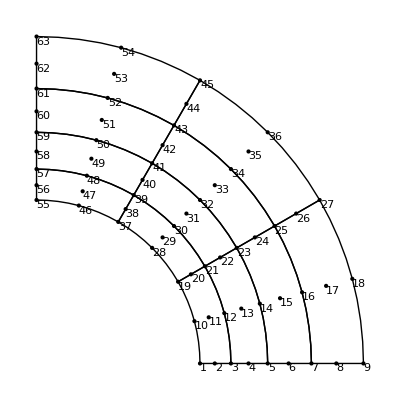

```mathematica
order=2;
serendipity=False;
{allcoords,nnodes,topol}=GenerateGridMesh[100,200,5,4,order];
linestopology=Flatten[Table[
{{topol[[i]][[1]],topol[[i]][[5]],topol[[i]][[2]]},
{topol[[i]][[2]],topol[[i]][[6]],topol[[i]][[3]]},
{topol[[i]][[3]],topol[[i]][[7]],topol[[i]][[4]]},
{topol[[i]][[4]],topol[[i]][[8]],topol[[i]][[1]]}
},{i,1,Length[topol]}],1];
Show[GenerateGraphics[nnodes,topol],Graphics[interpolatingQuadBezierCurveComplex[nnodes,linestopology]],ImageSize->Automatic]
x0=100;xf=200.;
y0=0;yf=0;
ndivs=100;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=100;yf=200;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
theta0=0;
thetaf=Pi/2;
r=100.;
searchpathinteriorhole=Table[{r Cos[theta],r Sin[theta]},{theta,theta0,thetaf,(thetaf-theta0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline];
idsleft=FindIds[nnodes,searchpathleftline];
idshole=FindIds[nnodes,searchpathinteriorhole];
```

```mathematica
planestress=False;
bodyforce=0;
ff=0.19209;
f[x_]:=ff;
fac={0.1/0.19209,0.14/0.19209,0.18/0.19209,0.19/0.19209,0.19209/0.19209}
FEXT=ContributeLineNewmanPressure[nnodes,order,idshole,r,f];
eltype=1;
order=2;
subst2={young->210,sigy->0.24,nu->0.3,G->young/(2(1+nu)),K->(young)/(3 (1-2nu))};
globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];
converge1={};
converge2={};
epspsolu={};
stresssolu={};
sol={};
solss={};
sol2={};
sol3={};
steps=10;
factor=1/steps;
displace=Table[0,{Length[nnodes] 2}];

lamb=1;
diff=10;
l=0.8;
counterout=1;
While[Abs[diff]>10^-8 && counterout≤30,
diverge=False;
convergevec1={};
convergevec2={};
Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;
temp=100;
tol=10^-6;
dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol,

epsppost={};
stressppost={};
globalcounter=1;
{KT,FINT}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
imposex=1;
imposey=2;

R=lamb  FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];
a=dwb.dwb;
b=2(dw+dws).dwb;
c=(dw+dws).(dw+dws)-l^2;
dlamb=Solve[a x^2 +b x+c==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];
AppendTo[convergevec1,{counter,err2}];
AppendTo[convergevec2,{counter,err1}];
Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[factor FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb];
counter++;
];
diff=Abs[lamb-lambn];
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];

AppendTo[converge1,convergevec1];
AppendTo[converge2,convergevec2];
AppendTo[sol,displace];
id=FindIds[nnodes,{{200,0}}][[1]];
AppendTo[sol2,{displace[[id 2-1]],ff lamb}];

(*AppendTo[sol2,{displace[[9 2-1]], ff fac[[i]]}];*)
AppendTo[sol3,epspvec];
factor+=1/steps;
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
];
```

{0.520589,0.728825,0.937061,0.98912,1.}

i = 1 | lamb = 1 | lambn = 0.998671 | diff = 10

Iteration number = 1  |R|/|FE| =  10.  |Δu|/|u| = 1.  |R| =  12.7299 |dw| = 0.8 | dlamb = -0.275035 | lamb = 0.724965

Iteration number = 2  |R|/|FE| =  2.50711  |Δu|/|u| = 0.00448861  |R| =  3.19152 |dw| = 0.00359089 | dlamb = -0.0352691 | lamb = 0.689695

Iteration number = 3  |R|/|FE| =  0.027942  |Δu|/|u| = 0.0000485249  |R| =  0.0355699 |dw| = 0.00003882 | dlamb = -0.000140221 | lamb = 0.689555

Iteration number = 4  |R|/|FE| =  3.67417×10^-6  |Δu|/|u| = 1.05171×10^-8  |R| =  4.67718×10^-6 |dw| = 8.41368×10^-9 | dlamb = -1.52345×10^-8 | lamb = 0.689555

i = 2 | lamb = 0.689555 | lambn = 1 | diff = 0.310445

Iteration number = 1  |R|/|FE| =  0.000910105  |Δu|/|u| = 0.500044  |R| =  0.00231711 |dw| = 0.8 | dlamb = 0.481865 | lamb = 1.17142

Iteration number = 2  |R|/|FE| =  3.10671  |Δu|/|u| = 0.0182155  |R| =  7.90964 |dw| = 0.0291334 | dlamb = -0.22962 | lamb = 0.9418

Iteration number = 3  |R|/|FE| =  0.0416466  |Δu|/|u| = 0.000226456  |R| =  0.106031 |dw| = 0.000362184 | dlamb = -0.000919149 | lamb = 0.940881

Iteration number = 4  |R|/|FE| =  8.98429×10^-6  |Δu|/|u| = 9.22782×10^-8  |R| =  0.0000228738 |dw| = 1.47586×10^-7 | dlamb = -1.06046×10^-7 | lamb = 0.940881

i = 3 | lamb = 0.940881 | lambn = 0.689555 | diff = 0.251326

Iteration number = 1  |R|/|FE| =  0.00880801  |Δu|/|u| = 0.333489  |R| =  0.0336375 |dw| = 0.8 | dlamb = 0.114607 | lamb = 1.05549

Iteration number = 2  |R|/|FE| =  1.26215  |Δu|/|u| = 0.00354845  |R| =  4.8201 |dw| = 0.00851212 | dlamb = -0.0576662 | lamb = 0.997822

Iteration number = 3  |R|/|FE| =  0.0138588  |Δu|/|u| = 0.0000566774  |R| =  0.0529262 |dw| = 0.000135959 | dlamb = -0.000231257 | lamb = 0.997591

Iteration number = 4  |R|/|FE| =  1.87716×10^-6  |Δu|/|u| = 1.29271×10^-7  |R| =  7.16884×10^-6 |dw| = 3.10098×10^-7 | dlamb = -1.91049×10^-8 | lamb = 0.997591

i = 4 | lamb = 0.997591 | lambn = 0.940881 | diff = 0.0567097

Iteration number = 1  |R|/|FE| =  0.0168027  |Δu|/|u| = 0.250109  |R| =  0.0855587 |dw| = 0.8 | dlamb = 0.0179094 | lamb = 1.0155

Iteration number = 2  |R|/|FE| =  0.717741  |Δu|/|u| = 0.000925091  |R| =  3.65471 |dw| = 0.00295899 | dlamb = -0.0159445 | lamb = 0.999556

Iteration number = 3  |R|/|FE| =  0.00429361  |Δu|/|u| = 0.0000131433  |R| =  0.0218629 |dw| = 0.0000420401 | dlamb = -0.0000515986 | lamb = 0.999504

Iteration number = 4  |R|/|FE| =  1.90459×10^-7  |Δu|/|u| = 1.49139×10^-8  |R| =  9.69811×10^-7 |dw| = 4.77034×10^-8 | dlamb = -1.91496×10^-9 | lamb = 0.999504

i = 5 | lamb = 0.999504 | lambn = 0.997591 | diff = 0.00191333

Iteration number = 1  |R|/|FE| =  0.0282794  |Δu|/|u| = 0.200076  |R| =  0.179997 |dw| = 0.8 | dlamb = 0.0028573 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0780051  |Δu|/|u| = 0.000466819  |R| =  0.496498 |dw| = 0.00186655 | dlamb = -0.00281628 | lamb = 0.999545

Iteration number = 3  |R|/|FE| =  0.0000439621  |Δu|/|u| = 3.27629×10^-6  |R| =  0.000279817 |dw| = 0.0000131001 | dlamb = -3.00441×10^-6 | lamb = 0.999542

Iteration number = 4  |R|/|FE| =  3.92472×10^-9  |Δu|/|u| = 5.40533×10^-10  |R| =  2.49806×10^-8 |dw| = 2.1613×10^-9 | dlamb = -9.06272×10^-13 | lamb = 0.999542

i = 6 | lamb = 0.999542 | lambn = 0.999504 | diff = 0.0000380129

Iteration number = 1  |R|/|FE| =  0.0244398  |Δu|/|u| = 0.166723  |R| =  0.18667 |dw| = 0.8 | dlamb = 0.00282058 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0650366  |Δu|/|u| = 0.000387575  |R| =  0.496746 |dw| = 0.00185973 | dlamb = -0.0028166 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000366618  |Δu|/|u| = 2.41686×10^-6  |R| =  0.000280021 |dw| = 0.000011597 | dlamb = -2.99893×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  3.26408×10^-9  |Δu|/|u| = 4.50073×10^-10  |R| =  2.49308×10^-8 |dw| = 2.15961×10^-9 | dlamb = -8.63672×10^-13 | lamb = 0.999543

i = 7 | lamb = 0.999543 | lambn = 0.999542 | diff = 9.78407×10^-7

Iteration number = 1  |R|/|FE| =  0.0209642  |Δu|/|u| = 0.1429  |R| =  0.18681 |dw| = 0.8 | dlamb = 0.00281988 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0557531  |Δu|/|u| = 0.000331667  |R| =  0.496812 |dw| = 0.00185677 | dlamb = -0.00281673 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000314275  |Δu|/|u| = 1.96105×10^-6  |R| =  0.000280049 |dw| = 0.0000109785 | dlamb = -2.99595×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  2.79472×10^-9  |Δu|/|u| = 3.85566×10^-10  |R| =  2.49036×10^-8 |dw| = 2.15851×10^-9 | dlamb = -8.4267×10^-13 | lamb = 0.999543

i = 8 | lamb = 0.999543 | lambn = 0.999543 | diff = 1.47345×10^-7

Iteration number = 1  |R|/|FE| =  0.0183436  |Δu|/|u| = 0.125034  |R| =  0.186809 |dw| = 0.8 | dlamb = 0.00281988 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0487887  |Δu|/|u| = 0.000289919  |R| =  0.496861 |dw| = 0.00185497 | dlamb = -0.0028168 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000275028  |Δu|/|u| = 1.65894×10^-6  |R| =  0.000280086 |dw| = 0.0000106143 | dlamb = -2.99419×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  2.44379×10^-9  |Δu|/|u| = 3.37222×10^-10  |R| =  2.48874×10^-8 |dw| = 2.15763×10^-9 | dlamb = -8.29699×10^-13 | lamb = 0.999543

i = 9 | lamb = 0.999543 | lambn = 0.999543 | diff = 8.42893×10^-8

Iteration number = 1  |R|/|FE| =  0.016305  |Δu|/|u| = 0.111139  |R| =  0.186805 |dw| = 0.8 | dlamb = 0.00281988 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0433709  |Δu|/|u| = 0.000257524  |R| =  0.496896 |dw| = 0.00185371 | dlamb = -0.00281683 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000244501  |Δu|/|u| = 1.4367×10^-6  |R| =  0.000280122 |dw| = 0.0000103416 | dlamb = -2.9931×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  2.17136×10^-9  |Δu|/|u| = 2.99733×10^-10  |R| =  2.48771×10^-8 |dw| = 2.15754×10^-9 | dlamb = -8.2157×10^-13 | lamb = 0.999543

i = 10 | lamb = 0.999543 | lambn = 0.999543 | diff = 5.54734×10^-8

Iteration number = 1  |R|/|FE| =  0.0146742  |Δu|/|u| = 0.100023  |R| =  0.186801 |dw| = 0.8 | dlamb = 0.00281986 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0390357  |Δu|/|u| = 0.000231648  |R| =  0.496921 |dw| = 0.00185276 | dlamb = -0.00281683 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000220074  |Δu|/|u| = 1.26476×10^-6  |R| =  0.000280153 |dw| = 0.0000101157 | dlamb = -2.9924×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  1.95369×10^-9  |Δu|/|u| = 2.6971×10^-10  |R| =  2.48703×10^-8 |dw| = 2.15718×10^-9 | dlamb = -8.15625×10^-13 | lamb = 0.999543

i = 11 | lamb = 0.999543 | lambn = 0.999543 | diff = 3.76516×10^-8

Iteration number = 1  |R|/|FE| =  0.0133398  |Δu|/|u| = 0.0909281  |R| =  0.186796 |dw| = 0.8 | dlamb = 0.00281983 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0354882  |Δu|/|u| = 0.000210502  |R| =  0.496937 |dw| = 0.00185203 | dlamb = -0.00281681 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000200085  |Δu|/|u| = 1.12769×10^-6  |R| =  0.000280176 |dw| = 9.92162×10^-6 | dlamb = -2.99194×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  1.77573×10^-9  |Δu|/|u| = 2.45186×10^-10  |R| =  2.48654×10^-8 |dw| = 2.15718×10^-9 | dlamb = -8.11441×10^-13 | lamb = 0.999543

i = 12 | lamb = 0.999543 | lambn = 0.999543 | diff = 2.6131×10^-8

Iteration number = 1  |R|/|FE| =  0.0122279  |Δu|/|u| = 0.0833495  |R| =  0.186792 |dw| = 0.8 | dlamb = 0.00281979 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0325315  |Δu|/|u| = 0.000192897  |R| =  0.496948 |dw| = 0.00185145 | dlamb = -0.00281678 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000183422  |Δu|/|u| = 1.01608×10^-6  |R| =  0.000280194 |dw| = 9.75247×10^-6 | dlamb = -2.99163×10^-6 | lamb = 0.999543

Iteration number = 4  |R|/|FE| =  1.62755×10^-9  |Δu|/|u| = 2.24766×10^-10  |R| =  2.48623×10^-8 |dw| = 2.15734×10^-9 | dlamb = -8.08064×10^-13 | lamb = 0.999543

i = 13 | lamb = 0.999543 | lambn = 0.999543 | diff = 1.84727×10^-8

Iteration number = 1  |R|/|FE| =  0.0112871  |Δu|/|u| = 0.076937  |R| =  0.186788 |dw| = 0.8 | dlamb = 0.00281974 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0300294  |Δu|/|u| = 0.000178012  |R| =  0.496953 |dw| = 0.00185099 | dlamb = -0.00281673 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.000016932  |Δu|/|u| = 9.23635×10^-7  |R| =  0.000280206 |dw| = 9.60405×10^-6 | dlamb = -2.99141×10^-6 | lamb = 0.999543

i = 14 | lamb = 0.999543 | lambn = 0.999543 | diff = 1.32608×10^-8

Iteration number = 1  |R|/|FE| =  0.0104798  |Δu|/|u| = 0.0726217  |R| =  0.186769 |dw| = 0.8 | dlamb = 0.00300045 | lamb = 1.00254

Iteration number = 2  |R|/|FE| =  0.0424527  |Δu|/|u| = 0.00501404  |R| =  0.756587 |dw| = 0.0553957 | dlamb = -0.00308608 | lamb = 0.999458

Iteration number = 3  |R|/|FE| =  0.0115413  |Δu|/|u| = 0.00672342  |R| =  0.205688 |dw| = 0.0745431 | dlamb = -5.82223×10^-6 | lamb = 0.999452

Iteration number = 4  |R|/|FE| =  0.00236125  |Δu|/|u| = 0.0260191  |R| =  0.0420819 |dw| = 0.291028 | dlamb = 0.000159422 | lamb = 0.999611

Iteration number = 5  |R|/|FE| =  0.0031429  |Δu|/|u| = 0.0123184  |R| =  0.0560123 |dw| = 0.137942 | dlamb = -0.0000572797 | lamb = 0.999554

Iteration number = 6  |R|/|FE| =  0.000363517  |Δu|/|u| = 0.000993135  |R| =  0.00647855 |dw| = 0.0111212 | dlamb = -0.0000105788 | lamb = 0.999543

Iteration number = 7  |R|/|FE| =  3.75273×10^-6  |Δu|/|u| = 8.80486×10^-6  |R| =  0.0000668807 |dw| = 0.0000985977 | dlamb = -9.19653×10^-8 | lamb = 0.999543

Iteration number = 8  |R|/|FE| =  4.14373×10^-10  |Δu|/|u| = 1.01971×10^-9  |R| =  7.3849×10^-9 |dw| = 1.14188×10^-8 | dlamb = -9.51995×10^-12 | lamb = 0.999543

i = 15 | lamb = 0.999543 | lambn = 0.999543 | diff = 1.90609×10^-8

Iteration number = 1  |R|/|FE| =  0.00978177  |Δu|/|u| = 0.0666773  |R| =  0.186781 |dw| = 0.8 | dlamb = 0.00281963 | lamb = 1.00236

Iteration number = 2  |R|/|FE| =  0.0260256  |Δu|/|u| = 0.000154222  |R| =  0.496956 |dw| = 0.00185036 | dlamb = -0.00281664 | lamb = 0.999546

Iteration number = 3  |R|/|FE| =  0.0000146751  |Δu|/|u| = 7.83154×10^-7  |R| =  0.000280219 |dw| = 9.39634×10^-6 | dlamb = -2.99114×10^-6 | lamb = 0.999543

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

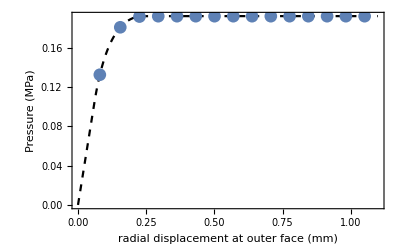

```mathematica
data=Table[i,{i,0,0.192,0.001}];
Clear[f]
eq[P_]:=(Log[c/a]+0.5 (1-c^2/b^2))-P/Y;
ub0[P_]:=2 P b/(young (b^2/a^2-1))(1-nu^2);
ub1[c_]:=Y c^2 (1-nu^2)/(young b);
Clear[a,b,c,nu,sigy,young]
subst={Y->2 sigy/Sqrt[3],young->210, b->200,a->100,sigy->0.240,nu->0.3};
P0=Y/2 (1 - a^2 /b^2) //.subst;
f[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,0.2}][[1,2]];
solu=ub1[solc]//.subst;
solu
]
computec[P_]:=Block[{},
eqc=eq[P]//.subst;
solc=FindRoot[eqc,{c,100}][[1,2]]
]
ComputeAnalyticalStress[r_,P_]:=Block[{a=100,b=200,sigy=0.24,sigr,sigt,cc,Y},
Y=2 sigy/Sqrt[3];
cc=computec[P];
If[a<=r<=cc,
sigr=Y(-0.5 -Log[cc/r]+cc^2 /(2 b^2));
sigt=Y(0.5 -Log[cc/r]+cc^2 /(2 b^2));
];
If[cc<=r≤b,
sigr=-Y cc^2 /(2 b^2)(b^2 / r^2 -1);
sigt=Y cc^2 /(2 b^2)(b^2 / r^2 +1);
];
{sigr,sigt}
]
u[P_]:=If[P<P0,ub0[P],f[P]]
tab=Table[{u[data[[i]]]//.subst ,data[[i]]},{i,1,Length[data]}];
AppendTo[tab,{0.3,0.19208}];
AppendTo[tab,{1.1,0.19208}];
a=ListLinePlot[tab,PlotStyle->{Black,Dashed}];
b=ListPlot[sol2,PlotMarkers->{Automatic,13}];
Show[a,b,PlotRange->All,PlotLegends->Placed[{"Analytical Solution", "Present Solution"},{0.79,0.11}],Frame->True,FrameLabel->{"radial displacement at outer face (mm)","Pressure (MPa)"}]
```